#### k = 3 count 1s

```mathematica
ParallelTable[SeedRandom[221350 + i];
AdaptiveCellularAutomaton[<|"Rule"->{0, 3, 1}, "Depth"->1000, 
"MutationFunction"->(RandomRuleMutation[#Rule, 1]&),
"FitnessFunction"-> (-Total[Abs[Table[2i - Count[#, 1]&[CellularAutomaton[#1, {Append[Table[1, i], 2], 0}, {{{60}}}]] , {i, 5}]]]&)|>, "Final"], {i , 200}]
```

```mathematica
out = {<|"Rule"->{4019820974163,3,1},"Fitness"->-5|>,<|"Rule"->{4007514803679,3,1},"Fitness"->-3|>,<|"Rule"->{7097049833943,3,1},"Fitness"->0|>,<|"Rule"->{1933779937377,3,1},"Fitness"->-3|>,<|"Rule"->{6262239456594,3,1},"Fitness"->-8|>,<|"Rule"->{2832951536760,3,1},"Fitness"->-2|>,<|"Rule"->{4970276989125,3,1},"Fitness"->-2|>,<|"Rule"->{6448936441437,3,1},"Fitness"->-2|>,<|"Rule"->{5102087061960,3,1},"Fitness"->-4|>,<|"Rule"->{6323332765041,3,1},"Fitness"->0|>,<|"Rule"->{4429829714646,3,1},"Fitness"->-4|>,<|"Rule"->{2430896849307,3,1},"Fitness"->-3|>,<|"Rule"->{4164980620941,3,1},"Fitness"->-4|>,<|"Rule"->{5523384175257,3,1},"Fitness"->-2|>,<|"Rule"->{174613146312,3,1},"Fitness"->-5|>,<|"Rule"->{2956118150880,3,1},"Fitness"->-5|>,<|"Rule"->{1682123971635,3,1},"Fitness"->-4|>,<|"Rule"->{464160639960,3,1},"Fitness"->-3|>,<|"Rule"->{2758339881552,3,1},"Fitness"->-2|>,<|"Rule"->{2756459261439,3,1},"Fitness"->-2|>,<|"Rule"->{4594716666657,3,1},"Fitness"->-4|>,<|"Rule"->{726072833520,3,1},"Fitness"->-6|>,<|"Rule"->{3458310352125,3,1},"Fitness"->0|>,<|"Rule"->{5650493886054,3,1},"Fitness"->-6|>,<|"Rule"->{4276561891629,3,1},"Fitness"->0|>,<|"Rule"->{2388881346603,3,1},"Fitness"->-6|>,<|"Rule"->{2438157855825,3,1},"Fitness"->-8|>,<|"Rule"->{3475516566996,3,1},"Fitness"->-8|>,<|"Rule"->{7600575711162,3,1},"Fitness"->-4|>,<|"Rule"->{1416819657153,3,1},"Fitness"->-4|>,<|"Rule"->{7024282169958,3,1},"Fitness"->-3|>,<|"Rule"->{5970699358779,3,1},"Fitness"->-4|>,<|"Rule"->{4264993540941,3,1},"Fitness"->-3|>,<|"Rule"->{139747926960,3,1},"Fitness"->-3|>,<|"Rule"->{2639535809052,3,1},"Fitness"->-4|>,<|"Rule"->{7030004314893,3,1},"Fitness"->-4|>,<|"Rule"->{3394007752062,3,1},"Fitness"->-2|>,<|"Rule"->{2782096402374,3,1},"Fitness"->-5|>,<|"Rule"->{4215845285088,3,1},"Fitness"->-4|>,<|"Rule"->{371202691944,3,1},"Fitness"->-1|>,<|"Rule"->{3046597784370,3,1},"Fitness"->-3|>,<|"Rule"->{1306314229776,3,1},"Fitness"->-5|>,<|"Rule"->{2167932258642,3,1},"Fitness"->-5|>,<|"Rule"->{3090725759274,3,1},"Fitness"->-2|>,<|"Rule"->{1293918487857,3,1},"Fitness"->-3|>,<|"Rule"->{7077218547402,3,1},"Fitness"->-10|>,<|"Rule"->{2047445795355,3,1},"Fitness"->-1|>,<|"Rule"->{4096192113690,3,1},"Fitness"->-2|>,<|"Rule"->{5999482359702,3,1},"Fitness"->0|>,<|"Rule"->{3281159866878,3,1},"Fitness"->-9|>,<|"Rule"->{2323671178305,3,1},"Fitness"->-3|>,<|"Rule"->{453427364901,3,1},"Fitness"->0|>,<|"Rule"->{238012673793,3,1},"Fitness"->0|>,<|"Rule"->{3194014631421,3,1},"Fitness"->-3|>,<|"Rule"->{6425947950885,3,1},"Fitness"->-4|>,<|"Rule"->{5439347795277,3,1},"Fitness"->-3|>,<|"Rule"->{3434339162295,3,1},"Fitness"->-5|>,<|"Rule"->{521897335890,3,1},"Fitness"->-4|>,<|"Rule"->{7447277248527,3,1},"Fitness"->-2|>,<|"Rule"->{774694375644,3,1},"Fitness"->-2|>,<|"Rule"->{821794851000,3,1},"Fitness"->-4|>,<|"Rule"->{2257949952108,3,1},"Fitness"->-2|>,<|"Rule"->{2328697058541,3,1},"Fitness"->-4|>,<|"Rule"->{5530848304482,3,1},"Fitness"->-6|>,<|"Rule"->{3923292122442,3,1},"Fitness"->-1|>,<|"Rule"->{7599919798707,3,1},"Fitness"->-4|>,<|"Rule"->{4209425020050,3,1},"Fitness"->-5|>,<|"Rule"->{7032448570566,3,1},"Fitness"->-2|>,<|"Rule"->{697526397165,3,1},"Fitness"->-3|>,<|"Rule"->{1743656792952,3,1},"Fitness"->-4|>,<|"Rule"->{6446080004886,3,1},"Fitness"->-6|>,<|"Rule"->{4000870204611,3,1},"Fitness"->-2|>,<|"Rule"->{5025721731384,3,1},"Fitness"->-1|>,<|"Rule"->{4219125791031,3,1},"Fitness"->-6|>,<|"Rule"->{7331957331276,3,1},"Fitness"->-3|>,<|"Rule"->{1528496371185,3,1},"Fitness"->-5|>,<|"Rule"->{3936092991030,3,1},"Fitness"->-4|>,<|"Rule"->{5289540798894,3,1},"Fitness"->-4|>,<|"Rule"->{1850690821023,3,1},"Fitness"->-2|>,<|"Rule"->{5294850501525,3,1},"Fitness"->-4|>,<|"Rule"->{6018877749210,3,1},"Fitness"->-4|>,<|"Rule"->{2514202860243,3,1},"Fitness"->0|>,<|"Rule"->{6534620033070,3,1},"Fitness"->0|>,<|"Rule"->{6925935352086,3,1},"Fitness"->-4|>,<|"Rule"->{60717317298,3,1},"Fitness"->-5|>,<|"Rule"->{432104526711,3,1},"Fitness"->-1|>,<|"Rule"->{2273393941059,3,1},"Fitness"->-3|>,<|"Rule"->{6524508923205,3,1},"Fitness"->-3|>,<|"Rule"->{532406288715,3,1},"Fitness"->-5|>,<|"Rule"->{2182998349500,3,1},"Fitness"->-6|>,<|"Rule"->{1925297127135,3,1},"Fitness"->-2|>,<|"Rule"->{2964067652586,3,1},"Fitness"->-4|>,<|"Rule"->{4527410780820,3,1},"Fitness"->-2|>,<|"Rule"->{4134101171784,3,1},"Fitness"->0|>,<|"Rule"->{4771933031313,3,1},"Fitness"->-3|>,<|"Rule"->{4213760615424,3,1},"Fitness"->-4|>,<|"Rule"->{1473200881209,3,1},"Fitness"->-5|>,<|"Rule"->{4583138101341,3,1},"Fitness"->-3|>,<|"Rule"->{1998138092529,3,1},"Fitness"->-3|>,<|"Rule"->{3719928237786,3,1},"Fitness"->-4|>,<|"Rule"->{1768764482406,3,1},"Fitness"->-3|>,<|"Rule"->{2011071132474,3,1},"Fitness"->-4|>,<|"Rule"->{5163526590639,3,1},"Fitness"->-5|>,<|"Rule"->{4258638671724,3,1},"Fitness"->-6|>,<|"Rule"->{5316607284441,3,1},"Fitness"->-2|>,<|"Rule"->{4666498958850,3,1},"Fitness"->-5|>,<|"Rule"->{2746647602889,3,1},"Fitness"->-3|>,<|"Rule"->{7577265732750,3,1},"Fitness"->-8|>,<|"Rule"->{5924665133226,3,1},"Fitness"->-6|>,<|"Rule"->{7425061452108,3,1},"Fitness"->-6|>,<|"Rule"->{3865096955604,3,1},"Fitness"->0|>,<|"Rule"->{7164900217695,3,1},"Fitness"->-3|>,<|"Rule"->{7327203574017,3,1},"Fitness"->-6|>,<|"Rule"->{7011459849441,3,1},"Fitness"->-3|>,<|"Rule"->{1228861180137,3,1},"Fitness"->-4|>,<|"Rule"->{5875644470982,3,1},"Fitness"->-5|>,<|"Rule"->{6301075989312,3,1},"Fitness"->-3|>,<|"Rule"->{2442433066515,3,1},"Fitness"->-4|>,<|"Rule"->{204782058660,3,1},"Fitness"->-2|>,<|"Rule"->{3460792643067,3,1},"Fitness"->-5|>,<|"Rule"->{6111792829698,3,1},"Fitness"->-6|>,<|"Rule"->{698743688553,3,1},"Fitness"->-4|>,<|"Rule"->{2052129282624,3,1},"Fitness"->-8|>,<|"Rule"->{6492456414711,3,1},"Fitness"->0|>,<|"Rule"->{6823954412745,3,1},"Fitness"->-2|>,<|"Rule"->{5242896440718,3,1},"Fitness"->-4|>,<|"Rule"->{7519127250057,3,1},"Fitness"->0|>,<|"Rule"->{5216050937655,3,1},"Fitness"->-7|>,<|"Rule"->{3058304861853,3,1},"Fitness"->0|>,<|"Rule"->{5415206879667,3,1},"Fitness"->-2|>,<|"Rule"->{3400484592870,3,1},"Fitness"->-3|>,<|"Rule"->{4481898100983,3,1},"Fitness"->-6|>,<|"Rule"->{2836926898479,3,1},"Fitness"->-3|>,<|"Rule"->{4529279481354,3,1},"Fitness"->-5|>,<|"Rule"->{289048054857,3,1},"Fitness"->-4|>,<|"Rule"->{703213930521,3,1},"Fitness"->-13|>,<|"Rule"->{2817073051011,3,1},"Fitness"->0|>,<|"Rule"->{6084761728989,3,1},"Fitness"->-5|>,<|"Rule"->{1926394467480,3,1},"Fitness"->-5|>,<|"Rule"->{66895017069,3,1},"Fitness"->-7|>,<|"Rule"->{3752732519370,3,1},"Fitness"->-8|>,<|"Rule"->{6919277283837,3,1},"Fitness"->-11|>,<|"Rule"->{5687196387018,3,1},"Fitness"->-4|>,<|"Rule"->{7097245077123,3,1},"Fitness"->-4|>,<|"Rule"->{1778674814103,3,1},"Fitness"->-4|>,<|"Rule"->{1518510179199,3,1},"Fitness"->-2|>,<|"Rule"->{5316494242623,3,1},"Fitness"->-5|>,<|"Rule"->{7364368010730,3,1},"Fitness"->-4|>,<|"Rule"->{1665240122427,3,1},"Fitness"->-4|>,<|"Rule"->{6081228113034,3,1},"Fitness"->-4|>,<|"Rule"->{3505878255624,3,1},"Fitness"->-4|>,<|"Rule"->{3866012682072,3,1},"Fitness"->-3|>,<|"Rule"->{6054373583760,3,1},"Fitness"->-4|>,<|"Rule"->{3053151522540,3,1},"Fitness"->-4|>,<|"Rule"->{6569638258662,3,1},"Fitness"->-3|>,<|"Rule"->{4514288983983,3,1},"Fitness"->-3|>,<|"Rule"->{4847169265482,3,1},"Fitness"->-1|>,<|"Rule"->{630252230025,3,1},"Fitness"->-7|>,<|"Rule"->{7125249632376,3,1},"Fitness"->-1|>,<|"Rule"->{5389714675122,3,1},"Fitness"->-3|>,<|"Rule"->{5060564200713,3,1},"Fitness"->-3|>,<|"Rule"->{3817493706909,3,1},"Fitness"->-1|>,<|"Rule"->{4319153071326,3,1},"Fitness"->-3|>,<|"Rule"->{4765892536755,3,1},"Fitness"->-1|>,<|"Rule"->{6216223712220,3,1},"Fitness"->-3|>,<|"Rule"->{3444725985600,3,1},"Fitness"->-6|>,<|"Rule"->{4075289012766,3,1},"Fitness"->-4|>,<|"Rule"->{6580922816463,3,1},"Fitness"->-8|>,<|"Rule"->{1923482780736,3,1},"Fitness"->-5|>,<|"Rule"->{3536296230015,3,1},"Fitness"->-4|>,<|"Rule"->{7306898944416,3,1},"Fitness"->-4|>,<|"Rule"->{451319502762,3,1},"Fitness"->-1|>,<|"Rule"->{5125584662955,3,1},"Fitness"->-7|>,<|"Rule"->{1066693365180,3,1},"Fitness"->-6|>,<|"Rule"->{3739025614395,3,1},"Fitness"->-5|>,<|"Rule"->{7574044921863,3,1},"Fitness"->-4|>,<|"Rule"->{5288563678107,3,1},"Fitness"->-4|>,<|"Rule"->{1949175366498,3,1},"Fitness"->-7|>,<|"Rule"->{3777354438369,3,1},"Fitness"->-4|>,<|"Rule"->{6822139687317,3,1},"Fitness"->-4|>,<|"Rule"->{477860896614,3,1},"Fitness"->-4|>,<|"Rule"->{1382466028824,3,1},"Fitness"->-5|>,<|"Rule"->{5393101784184,3,1},"Fitness"->-3|>,<|"Rule"->{4272696021387,3,1},"Fitness"->-5|>,<|"Rule"->{2471665484622,3,1},"Fitness"->-5|>,<|"Rule"->{6965858371836,3,1},"Fitness"->-1|>,<|"Rule"->{1326476015592,3,1},"Fitness"->-6|>,<|"Rule"->{2030841847047,3,1},"Fitness"->-4|>,<|"Rule"->{4057457466615,3,1},"Fitness"->-8|>,<|"Rule"->{5571869125617,3,1},"Fitness"->-3|>,<|"Rule"->{3849517277934,3,1},"Fitness"->-4|>,<|"Rule"->{22859750238,3,1},"Fitness"->-5|>,<|"Rule"->{2732955370134,3,1},"Fitness"->-10|>,<|"Rule"->{1873375498017,3,1},"Fitness"->-3|>,<|"Rule"->{4407542151741,3,1},"Fitness"->-6|>,<|"Rule"->{4572934613454,3,1},"Fitness"->-3|>,<|"Rule"->{7065426825,3,1},"Fitness"->-10|>,<|"Rule"->{1017139528578,3,1},"Fitness"->-5|>,<|"Rule"->{5672547813726,3,1},"Fitness"->-3|>,<|"Rule"->{3800611417539,3,1},"Fitness"->-2|>};
```

```mathematica
Select[Differences[Count[#, 1]&/@Table[CellularAutomaton[#Rule,{Append[Table[1, i], 2], 0},{{{200}}}], {i, 50}]]&/@out, AllTrue[#, # ==2&]&->"Index"]
```

{23,25,49,53,94,111,124,129}

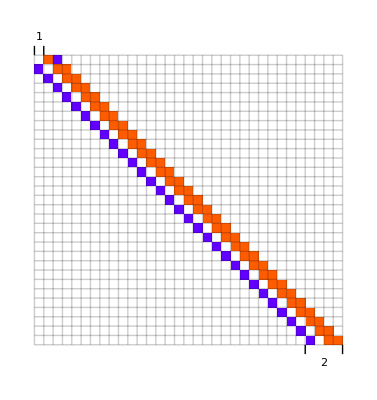
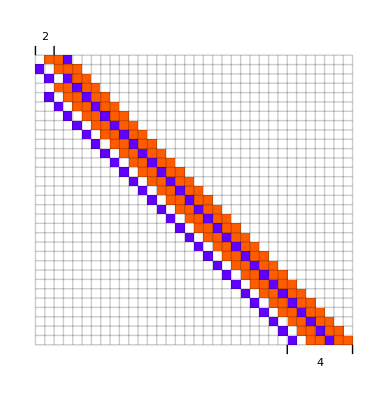
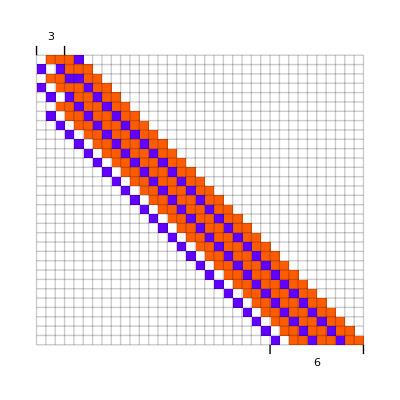
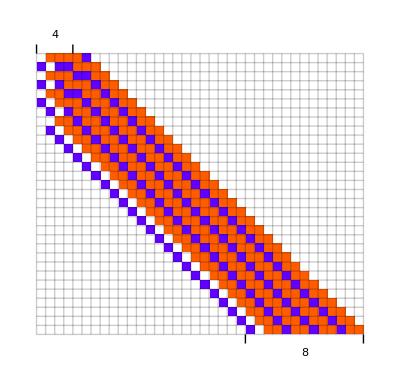
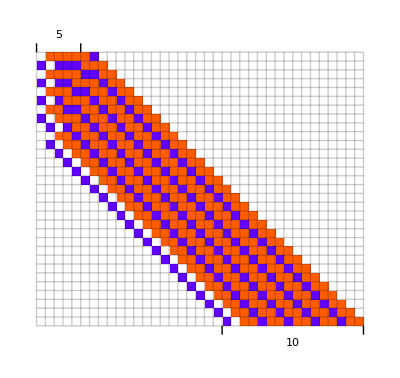
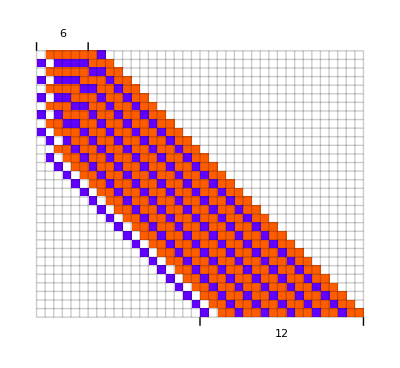
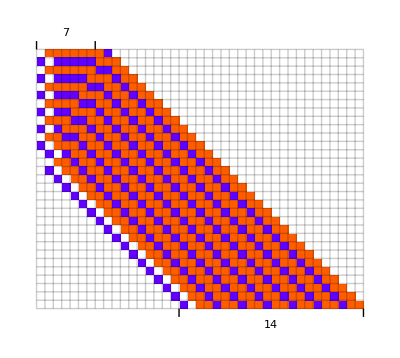
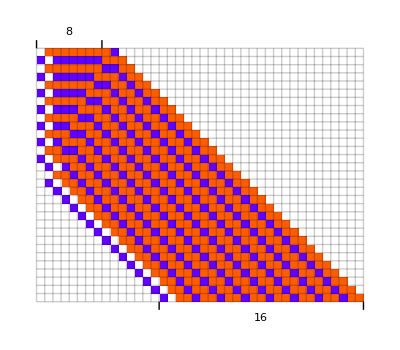

```mathematica
Row[Table[With[{ca = CellularAutomaton[#Rule,{Append[Table[1, i], 2], 0}, 30]},Show[ArrayPlot[ca, ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99],4->RGBColor[0, 0.56, 0],5->RGBColor[0, 0.56, 1]}, 
FrameTicksStyle->Directive[Thickness[.01], GrayLevel[.3]],Mesh->True, MeshStyle->Opacity[.2]],
Graphics[{Line[{{0, Length[ca]},{0, Length[ca] + 1}}],Line[{{0 + i, Length[ca]},{0 + i, Length[ca] + 1}}], Style[Text[ToString[i], {i /2, Length[ca] + 2}],10],
Sequence@@(Line[{{#, 0}, {#, -1}}]&/@MapAt[# -1&, nonzeroRange[Last[ca]], 1]),
Style[Text[ToString[Count[Last[ca], 1]], {Mean[MapAt[# -1&, nonzeroRange[Last[ca]], 1]], -2}],10]
}], PlotRange->All]], {i, 8}]&/@ out[[]]]
```

#### k = 4 count 1s

```mathematica
ParallelTable[SeedRandom[221350 + i];
AdaptiveCellularAutomaton[<|"Rule"->{0, 4, 1}, "Depth"->1000, 
"MutationFunction"->(RandomRuleMutation[#Rule, 1]&),
"FitnessFunction"-> (-Total[Abs[Table[2i - Count[#, 1]&[CellularAutomaton[#1, {Append[Table[1, i], 2], 0}, {{{60}}}]] , {i, 5}]]]&)|>, "Final"], {i , 200}]
```

{<|Rule→{196579914506444384531835626473012541580,4,1},Fitness→-2|>,<|Rule→{208584580858723759221892374223418879344,4,1},Fitness→-5|>,<|Rule→{270693018722199522587277128408144753172,4,1},Fitness→-2|>,<|Rule→{98551803433301119735064510308641940240,4,1},Fitness→0|>,<|Rule→{17340990303821833785488731114051541408,4,1},Fitness→-1|>,<|Rule→{102246957230960202412695568323594002568,4,1},Fitness→0|>,<|Rule→{34674535374049526751327132515383173572,4,1},Fitness→0|>,<|Rule→{291978123806383763860785338002907729956,4,1},Fitness→-1|>,<|Rule→{157986494589763084889096529935763030536,4,1},Fitness→-5|>,<|Rule→{90818990155608722937466992188895000880,4,1},Fitness→-4|>,<|Rule→{75852088012849122443921737259619848012,4,1},Fitness→-1|>,<|Rule→{1662752023589590759784184004546182368,4,1},Fitness→-1|>,<|Rule→{33490537987832886749624615810246967420,4,1},Fitness→-3|>,<|Rule→{128679032425237967394761276762692424748,4,1},Fitness→-2|>,<|Rule→{195872785751229799101561501308412232464,4,1},Fitness→0|>,<|Rule→{114373148829977414012840359529180515424,4,1},Fitness→-5|>,<|Rule→{149102760472455172978463548997897096240,4,1},Fitness→-3|>,<|Rule→{271146604799129867327159212314841153600,4,1},Fitness→-5|>,<|Rule→{186358759923340045164332337921090771456,4,1},Fitness→-3|>,<|Rule→{233973251989903915005074554624207536368,4,1},Fitness→-6|>,<|Rule→{218053267545305989495341385701407441072,4,1},Fitness→-3|>,<|Rule→{336639042993220088131258834307576248960,4,1},Fitness→-2|>,<|Rule→{21836521740777962069050781188404423884,4,1},Fitness→-4|>,<|Rule→{144150490640695351092344858321816165656,4,1},Fitness→-2|>,<|Rule→{203440412249849748694050916117428797956,4,1},Fitness→-3|>,<|Rule→{15601940150651531377316039334069277512,4,1},Fitness→-7|>,<|Rule→{234444557403428112428242662086312525872,4,1},Fitness→-4|>,<|Rule→{155364733219331253132706075539178457192,4,1},Fitness→-1|>,<|Rule→{48665612694933038413657518831047117344,4,1},Fitness→-3|>,<|Rule→{218673001839232765480151485737439835328,4,1},Fitness→-1|>,<|Rule→{42768568847682608116884281741101389988,4,1},Fitness→-2|>,<|Rule→{180951385967558823837047011851885889344,4,1},Fitness→-4|>,<|Rule→{202922429329752203335898398325496261712,4,1},Fitness→-1|>,<|Rule→{173715446328245127916845838786050709528,4,1},Fitness→-1|>,<|Rule→{303429041261539673353529610055739831820,4,1},Fitness→-4|>,<|Rule→{33034230351039143574594203889273614704,4,1},Fitness→0|>,<|Rule→{262625176138392466934347060424725202416,4,1},Fitness→-3|>,<|Rule→{193597814225446805737152238466843326000,4,1},Fitness→-4|>,<|Rule→{180779016405133651657392047587516797256,4,1},Fitness→-3|>,<|Rule→{57068092929069004711854340581315355744,4,1},Fitness→-4|>,<|Rule→{8987217563477841605307057115257414832,4,1},Fitness→-3|>,<|Rule→{63736400898545802336633021354063755552,4,1},Fitness→-1|>,<|Rule→{256796764536858736265418926532053174704,4,1},Fitness→-3|>,<|Rule→{245189897381236325112653850498409022080,4,1},Fitness→-6|>,<|Rule→{223578683691221384542856955509765661360,4,1},Fitness→-4|>,<|Rule→{81394857265029126331312784406379495724,4,1},Fitness→-2|>,<|Rule→{240904301173424462797845708198080833936,4,1},Fitness→-2|>,<|Rule→{199840554604448588306232169386935330832,4,1},Fitness→-2|>,<|Rule→{299329358976922332420339273946982214976,4,1},Fitness→-4|>,<|Rule→{103264345198607632239331530792526479404,4,1},Fitness→-2|>,<|Rule→{34689744245799370717416857610431768952,4,1},Fitness→-1|>,<|Rule→{156626390261695338652468562112588104848,4,1},Fitness→-2|>,<|Rule→{10933699916290939671314953583758218048,4,1},Fitness→-4|>,<|Rule→{68211029692965860827613087186032808520,4,1},Fitness→-2|>,<|Rule→{2794546880727189598903068939101086924,4,1},Fitness→-1|>,<|Rule→{135058112086188178770435469043763954520,4,1},Fitness→-3|>,<|Rule→{112336043332367976233403105965242842396,4,1},Fitness→-1|>,<|Rule→{297321621623701603048725828546452523696,4,1},Fitness→-4|>,<|Rule→{121210389815799449799776741725412567308,4,1},Fitness→0|>,<|Rule→{175227193692039052996479947224640425264,4,1},Fitness→-3|>,<|Rule→{277024146294646073463766695811740996100,4,1},Fitness→-2|>,<|Rule→{105684410155642110222758525881447684224,4,1},Fitness→-3|>,<|Rule→{154230012580060086430003818603771592980,4,1},Fitness→-4|>,<|Rule→{263788006691136037319599704312624692284,4,1},Fitness→-4|>,<|Rule→{311183169541565214031879362113500938640,4,1},Fitness→-3|>,<|Rule→{90721415397076812516921724932257795188,4,1},Fitness→-3|>,<|Rule→{155786174314964951555993849266408502284,4,1},Fitness→-8|>,<|Rule→{198623571039740729433419992129961476276,4,1},Fitness→-2|>,<|Rule→{319428077322150982017847793401640194432,4,1},Fitness→-2|>,<|Rule→{37462679113242609765271407598830025996,4,1},Fitness→-3|>,<|Rule→{99885131406932615569752205327377810368,4,1},Fitness→-6|>,<|Rule→{3904630305625019743548828367071184432,4,1},Fitness→-4|>,<|Rule→{94650129712636394562297014405445552588,4,1},Fitness→-2|>,<|Rule→{284883405021649139019284633581710357240,4,1},Fitness→-4|>,<|Rule→{147814261665601877622216742086073930988,4,1},Fitness→-3|>,<|Rule→{43341714057081942817987924684630598484,4,1},Fitness→-3|>,<|Rule→{194896040447802428773222385810362408016,4,1},Fitness→-1|>,<|Rule→{322677027783275992670891696643023120176,4,1},Fitness→-2|>,<|Rule→{209946866343802718636409775347370325888,4,1},Fitness→-1|>,<|Rule→{252460225469441486909505583412596217904,4,1},Fitness→-2|>,<|Rule→{101333066473586537540580352256183668664,4,1},Fitness→-2|>,<|Rule→{204265454225720615055950522279965814304,4,1},Fitness→-6|>,<|Rule→{119648981725669462746898859170002529596,4,1},Fitness→-3|>,<|Rule→{56441053235178639422285231042146377736,4,1},Fitness→-1|>,<|Rule→{238165037497780806036863040056636428932,4,1},Fitness→-3|>,<|Rule→{83935212971479827865514954617071417408,4,1},Fitness→0|>,<|Rule→{160155118810156951031967237784053779404,4,1},Fitness→-2|>,<|Rule→{31709518789598731478871357476744164208,4,1},Fitness→-8|>,<|Rule→{216145946782066366115733243764218236064,4,1},Fitness→-2|>,<|Rule→{154222098895723500274053612905600332860,4,1},Fitness→-4|>,<|Rule→{85746014995006750748627015550634045532,4,1},Fitness→-2|>,<|Rule→{111656695272420862261111911306346488896,4,1},Fitness→-3|>,<|Rule→{3943900405319276851836560265017324420,4,1},Fitness→-1|>,<|Rule→{27068303010899101572283820675845964148,4,1},Fitness→-4|>,<|Rule→{192279449561868235809965592182205135968,4,1},Fitness→-5|>,<|Rule→{275554503628457069265890047280452420400,4,1},Fitness→-2|>,<|Rule→{182694371110076724157416673132452228160,4,1},Fitness→0|>,<|Rule→{79995153050029811101496025670921831984,4,1},Fitness→-1|>,<|Rule→{6064928216174665838049536139386277808,4,1},Fitness→-2|>,<|Rule→{329651495630387017835756928371099118400,4,1},Fitness→-2|>,<|Rule→{329941707304153015909669134523545110788,4,1},Fitness→-3|>,<|Rule→{57885265610649161545682599764933971232,4,1},Fitness→-2|>,<|Rule→{330589329986364532833712787412930104576,4,1},Fitness→-1|>,<|Rule→{175379905494515286337772543505768461336,4,1},Fitness→-1|>,<|Rule→{1096147435759750064597122959780671544,4,1},Fitness→-2|>,<|Rule→{228894486969812259321453605190848153520,4,1},Fitness→-6|>,<|Rule→{256527294992448658549228960564495745712,4,1},Fitness→-1|>,<|Rule→{24212656724016599909219909218992529264,4,1},Fitness→-1|>,<|Rule→{8828701360394713743792925503785541832,4,1},Fitness→-4|>,<|Rule→{100961618860866362997308917573933381908,4,1},Fitness→-1|>,<|Rule→{292430283862131886970936475804684596188,4,1},Fitness→-5|>,<|Rule→{202502010246888909343918413264023827572,4,1},Fitness→-4|>,<|Rule→{270328601606399807951726987078328434916,4,1},Fitness→-4|>,<|Rule→{18612527466882319426697319592443250632,4,1},Fitness→-4|>,<|Rule→{204997659487346183217141656164694638880,4,1},Fitness→-5|>,<|Rule→{297144741786139903554381709280879141404,4,1},Fitness→-4|>,<|Rule→{207907910070416827546694815502563282000,4,1},Fitness→-1|>,<|Rule→{3398158384239329143271951925646388736,4,1},Fitness→-3|>,<|Rule→{201907081615711181819747733373018976492,4,1},Fitness→-1|>,<|Rule→{273640955004958063513321919872494634768,4,1},Fitness→-3|>,<|Rule→{162827550353376782811531525093096349756,4,1},Fitness→-3|>,<|Rule→{56260744118009107857749286392766398096,4,1},Fitness→-3|>,<|Rule→{239623254563314995591584607708469267684,4,1},Fitness→-2|>,<|Rule→{95068760288282085099385692537815794804,4,1},Fitness→-1|>,<|Rule→{65734757524914079708947224674990538248,4,1},Fitness→-3|>,<|Rule→{8990938652440631738733641067606892576,4,1},Fitness→-4|>,<|Rule→{304327256531187060289152490851232022540,4,1},Fitness→0|>,<|Rule→{3181198758824237563008251987596642420,4,1},Fitness→0|>,<|Rule→{338657989464758445223721413602984770624,4,1},Fitness→-2|>,<|Rule→{234677575924186344195805277758648813568,4,1},Fitness→-2|>,<|Rule→{199037900478833538970307637740521211392,4,1},Fitness→0|>,<|Rule→{55879245913336070978113407711283077936,4,1},Fitness→-3|>,<|Rule→{98245173282879428115456253746117215428,4,1},Fitness→0|>,<|Rule→{278118279828502604569163001065238172768,4,1},Fitness→-2|>,<|Rule→{81677747227611359867974563834150256896,4,1},Fitness→-2|>,<|Rule→{141578234407685017858971415924616462772,4,1},Fitness→-4|>,<|Rule→{189717647327228864375489024342759801944,4,1},Fitness→0|>,<|Rule→{308062644208440084013187286516442676000,4,1},Fitness→-3|>,<|Rule→{103947041837871974293948071550715298148,4,1},Fitness→-2|>,<|Rule→{96313132436644096634921061330376183820,4,1},Fitness→0|>,<|Rule→{24163070876091621860385664857080941568,4,1},Fitness→0|>,<|Rule→{164741698145685166978946253906349179144,4,1},Fitness→-2|>,<|Rule→{149519075305058247496788123548449277196,4,1},Fitness→-4|>,<|Rule→{266030806457048097598505053338252640532,4,1},Fitness→-2|>,<|Rule→{74184611307385846479721363031684546948,4,1},Fitness→0|>,<|Rule→{5959035698476053156909196355989930036,4,1},Fitness→-3|>,<|Rule→{236853973577179866893768633746875093776,4,1},Fitness→-4|>,<|Rule→{338956446692131522975365576010057358388,4,1},Fitness→-2|>,<|Rule→{195580484803813280281859920277013503520,4,1},Fitness→-6|>,<|Rule→{323336107940091513841522649563527962240,4,1},Fitness→-1|>,<|Rule→{164957494189883435633148724428881717384,4,1},Fitness→0|>,<|Rule→{128659326637912409061939309815248826416,4,1},Fitness→-3|>,<|Rule→{75454027713481572136369888062492443040,4,1},Fitness→-2|>,<|Rule→{144250488920836611444851926920852453520,4,1},Fitness→-2|>,<|Rule→{176253034137545083313442005902394049548,4,1},Fitness→-1|>,<|Rule→{255288667957308854989378251751074853664,4,1},Fitness→-3|>,<|Rule→{42238836989535450587599069173278328084,4,1},Fitness→-2|>,<|Rule→{95524079786910692701196153893892755420,4,1},Fitness→-2|>,<|Rule→{136913174884639762849541200738778807808,4,1},Fitness→-4|>,<|Rule→{91191721582223022423811523262969612856,4,1},Fitness→-3|>,<|Rule→{306333204541184152999154811696990364884,4,1},Fitness→-4|>,<|Rule→{326377331216849329288246991433877815616,4,1},Fitness→-6|>,<|Rule→{318625505579416311843017141943790739564,4,1},Fitness→0|>,<|Rule→{219993719048235375949762207872324018320,4,1},Fitness→-4|>,<|Rule→{182873761183374832646045891086170268804,4,1},Fitness→-2|>,<|Rule→{293686948546936613987049606645933755908,4,1},Fitness→-1|>,<|Rule→{317543495503461292624436546110119516180,4,1},Fitness→-1|>,<|Rule→{293170528399254982090305589797252203008,4,1},Fitness→-5|>,<|Rule→{307799449125218150798770342430617882224,4,1},Fitness→-1|>,<|Rule→{46876991977428520971786935409150824236,4,1},Fitness→0|>,<|Rule→{289205859377641998353367793427144018808,4,1},Fitness→-3|>,<|Rule→{93940258782956023895626913548157910596,4,1},Fitness→-2|>,<|Rule→{614182060072709889600949596287434780,4,1},Fitness→-2|>,<|Rule→{101962395648151274884844933993550059552,4,1},Fitness→-3|>,<|Rule→{188449253251321901509965501545822781836,4,1},Fitness→-5|>,<|Rule→{5278376571708593836101767500899927108,4,1},Fitness→0|>,<|Rule→{214079799959111036927533444562513052620,4,1},Fitness→-3|>,<|Rule→{217825782729701691543602804218554024048,4,1},Fitness→-2|>,<|Rule→{250590482406841565447858414896290212364,4,1},Fitness→-2|>,<|Rule→{110687167376359701193275675606761443448,4,1},Fitness→-1|>,<|Rule→{153484659799518330686910821108215138608,4,1},Fitness→-5|>,<|Rule→{209133406788730715243968972363595335120,4,1},Fitness→-3|>,<|Rule→{47890757666700158817064601299050233088,4,1},Fitness→-2|>,<|Rule→{252181304630930760514552910423024436420,4,1},Fitness→-1|>,<|Rule→{162016310228498291539093047304215463680,4,1},Fitness→-6|>,<|Rule→{315429605234092921864094176163125770376,4,1},Fitness→-3|>,<|Rule→{84133404523139505408327867824561489116,4,1},Fitness→-2|>,<|Rule→{43544892206271732265457785120957361968,4,1},Fitness→0|>,<|Rule→{243890053191576794307940161655727803092,4,1},Fitness→-4|>,<|Rule→{151629614614342917935780259546280902540,4,1},Fitness→-3|>,<|Rule→{126601801925510321158768495759955827712,4,1},Fitness→0|>,<|Rule→{85149829589722771119730336763250016264,4,1},Fitness→-2|>,<|Rule→{112395001120126742092716819942672295008,4,1},Fitness→-3|>,<|Rule→{47205995767695509859003261297943774144,4,1},Fitness→-6|>,<|Rule→{236357333803458442059104663325034873472,4,1},Fitness→-2|>,<|Rule→{233948833532009602785781777581012070912,4,1},Fitness→-4|>,<|Rule→{305351800370911993456336447285708439760,4,1},Fitness→-4|>,<|Rule→{113460027518342302642975211472473358836,4,1},Fitness→0|>,<|Rule→{85482181035169483767462264877710246528,4,1},Fitness→-3|>,<|Rule→{68358063416557583366339384871563299492,4,1},Fitness→-2|>}

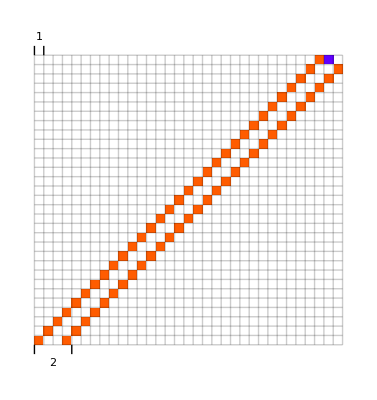
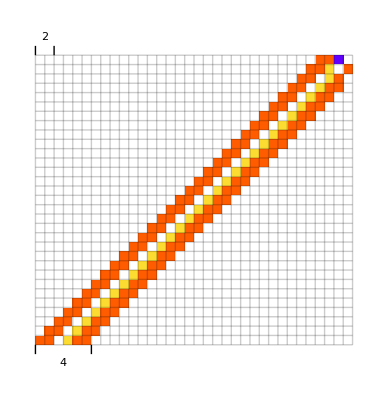
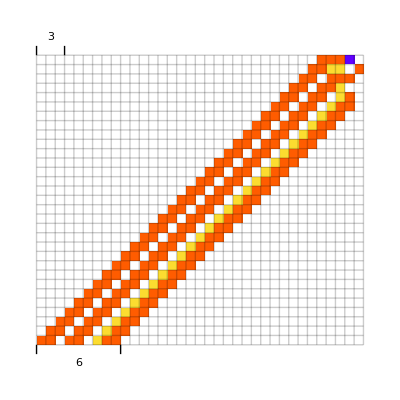
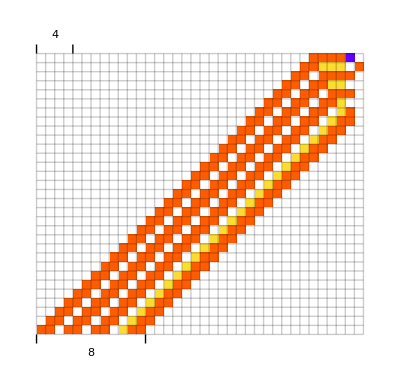
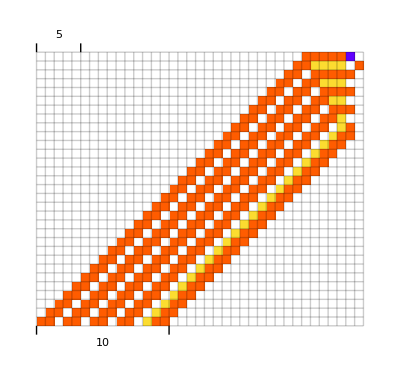
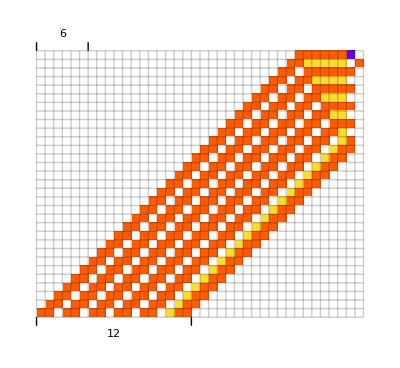
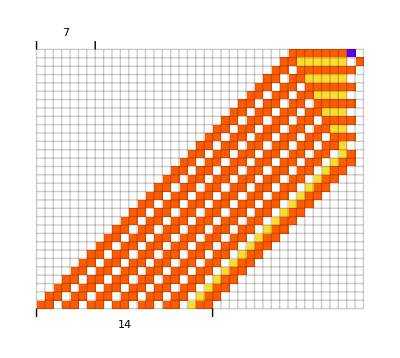
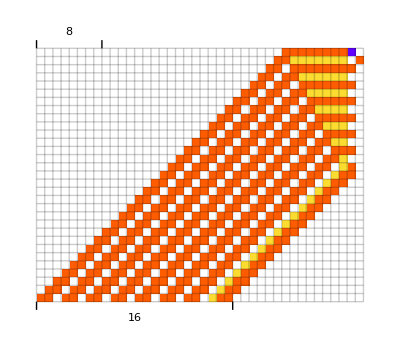

```mathematica
Row[Table[With[{ca = CellularAutomaton[#Rule,{Append[Table[1, i], 2], 0}, 30]},Show[ArrayPlot[ca, ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99],4->RGBColor[0, 0.56, 0],5->RGBColor[0, 0.56, 1]}, 
FrameTicksStyle->Directive[Thickness[.01], GrayLevel[.3]],Mesh->True, MeshStyle->Opacity[.2]],
Graphics[{Line[{{0, Length[ca]},{0, Length[ca] + 1}}],Line[{{0 + i, Length[ca]},{0 + i, Length[ca] + 1}}], Style[Text[ToString[i], {i /2, Length[ca] + 2}],10],
Sequence@@(Line[{{#, 0}, {#, -1}}]&/@MapAt[# -1&, nonzeroRange[Last[ca]], 1]),
Style[Text[ToString[Count[Last[ca], 1]], {Mean[MapAt[# -1&, nonzeroRange[Last[ca]], 1]], -2}],10]
}], PlotRange->All]], {i, 8}]&/@ [[Select[Differences[Count[#, 1]&/@Table[CellularAutomaton[#Rule,{Append[Table[1, i], 2], 0},{{{200}}}], {i, 50}]]&/@, AllTrue[#, # ==2&]&->"Index"]]]]
```

#### Weird ff that worked

```mathematica
ParallelTable[SeedRandom[222550 + i];
AdaptiveCellularAutomaton[<|"Rule"->{0, 3, 1}, "Depth"->1000, 
"MutationFunction"->(RandomRuleMutation[#Rule, 1]&),
"FitnessFunction"-> (-Total[Abs[Table[CenterArray[#, Max[Length[#],2i]&[#]] - CenterArray[Table[1, 2i+2], Max[Length[#],2i]]&[CellularAutomaton[#1, {Append[Table[1, i], 2], 0}, {{{60}}}]] , {i, 5}]], 2]&)|>, "Final"], {i , 200}]
```

{<|Rule→{531453409086,3,1},Fitness→-6|>,<|Rule→{1649509612626,3,1},Fitness→-11|>,<|Rule→{6064986840861,3,1},Fitness→-14|>,<|Rule→{6982242940071,3,1},Fitness→-6|>,<|Rule→{3712131072459,3,1},Fitness→-11|>,<|Rule→{1100099063319,3,1},Fitness→-1|>,<|Rule→{3166509606975,3,1},Fitness→-1|>,<|Rule→{4341297135135,3,1},Fitness→-2|>,<|Rule→{6797628898023,3,1},Fitness→-2|>,<|Rule→{6727760653671,3,1},Fitness→-5|>,<|Rule→{7374842609250,3,1},Fitness→-2|>,<|Rule→{5772633635790,3,1},Fitness→-12|>,<|Rule→{4412273143911,3,1},Fitness→-1|>,<|Rule→{6502990639815,3,1},Fitness→-9|>,<|Rule→{105055521669,3,1},Fitness→-8|>,<|Rule→{3809369478501,3,1},Fitness→-2|>,<|Rule→{3904766713296,3,1},Fitness→-6|>,<|Rule→{3857722499199,3,1},Fitness→-12|>,<|Rule→{113205098640,3,1},Fitness→-2|>,<|Rule→{6038529676821,3,1},Fitness→-6|>,<|Rule→{6047427417999,3,1},Fitness→-10|>,<|Rule→{118696886799,3,1},Fitness→-12|>,<|Rule→{3735907002222,3,1},Fitness→-8|>,<|Rule→{2083350111378,3,1},Fitness→-6|>,<|Rule→{3002734012146,3,1},Fitness→-11|>,<|Rule→{144652178241,3,1},Fitness→-11|>,<|Rule→{3277110862611,3,1},Fitness→-1|>,<|Rule→{402660037500,3,1},Fitness→-8|>,<|Rule→{715539494655,3,1},Fitness→0|>,<|Rule→{6368995983159,3,1},Fitness→-10|>,<|Rule→{6919666578102,3,1},Fitness→-2|>,<|Rule→{4286571993138,3,1},Fitness→-4|>,<|Rule→{5023693589400,3,1},Fitness→-1|>,<|Rule→{7390344873717,3,1},Fitness→0|>,<|Rule→{7508766703608,3,1},Fitness→-8|>,<|Rule→{6038373740004,3,1},Fitness→-4|>,<|Rule→{1531883609847,3,1},Fitness→-9|>,<|Rule→{2755213713327,3,1},Fitness→-7|>,<|Rule→{1087443626094,3,1},Fitness→-2|>,<|Rule→{6971523080319,3,1},Fitness→-13|>,<|Rule→{3499141054662,3,1},Fitness→-1|>,<|Rule→{2494684285191,3,1},Fitness→0|>,<|Rule→{6157024307823,3,1},Fitness→-9|>,<|Rule→{1145422651134,3,1},Fitness→-1|>,<|Rule→{3337447537056,3,1},Fitness→-2|>,<|Rule→{5127020275293,3,1},Fitness→-12|>,<|Rule→{7011361602288,3,1},Fitness→0|>,<|Rule→{3008513957490,3,1},Fitness→-6|>,<|Rule→{2043904729278,3,1},Fitness→-10|>,<|Rule→{3839275178292,3,1},Fitness→-10|>,<|Rule→{4368464926674,3,1},Fitness→-3|>,<|Rule→{3743952848238,3,1},Fitness→-15|>,<|Rule→{1836605143800,3,1},Fitness→-1|>,<|Rule→{1652297560806,3,1},Fitness→-2|>,<|Rule→{3730274106021,3,1},Fitness→-8|>,<|Rule→{3064316155293,3,1},Fitness→-2|>,<|Rule→{5970688504272,3,1},Fitness→-15|>,<|Rule→{6956715460341,3,1},Fitness→-3|>,<|Rule→{6980572127253,3,1},Fitness→-14|>,<|Rule→{3460636537425,3,1},Fitness→-8|>,<|Rule→{6181477693371,3,1},Fitness→-1|>,<|Rule→{3429129450777,3,1},Fitness→-9|>,<|Rule→{1558068893757,3,1},Fitness→-2|>,<|Rule→{1020627489600,3,1},Fitness→-13|>,<|Rule→{1983099521700,3,1},Fitness→-9|>,<|Rule→{1997489508105,3,1},Fitness→-2|>,<|Rule→{3439731862809,3,1},Fitness→-1|>,<|Rule→{3530385599571,3,1},Fitness→-6|>,<|Rule→{2278727869338,3,1},Fitness→-6|>,<|Rule→{957265261122,3,1},Fitness→-2|>,<|Rule→{3310498068318,3,1},Fitness→-11|>,<|Rule→{7513553957706,3,1},Fitness→-3|>,<|Rule→{1050136526214,3,1},Fitness→-1|>,<|Rule→{5926492452243,3,1},Fitness→-2|>,<|Rule→{2059115931063,3,1},Fitness→-12|>,<|Rule→{1079336985570,3,1},Fitness→-2|>,<|Rule→{5660411305482,3,1},Fitness→-5|>,<|Rule→{4603318216803,3,1},Fitness→-1|>,<|Rule→{5912961438447,3,1},Fitness→-6|>,<|Rule→{4186632921939,3,1},Fitness→-11|>,<|Rule→{4624005873276,3,1},Fitness→-6|>,<|Rule→{7130502179946,3,1},Fitness→-8|>,<|Rule→{5072832873048,3,1},Fitness→-2|>,<|Rule→{4658685882126,3,1},Fitness→-3|>,<|Rule→{2839575663333,3,1},Fitness→-6|>,<|Rule→{3533468082159,3,1},Fitness→-4|>,<|Rule→{4105152716895,3,1},Fitness→-10|>,<|Rule→{1002455181531,3,1},Fitness→-4|>,<|Rule→{4722024014298,3,1},Fitness→-10|>,<|Rule→{5852452457424,3,1},Fitness→-1|>,<|Rule→{6983332794102,3,1},Fitness→-1|>,<|Rule→{4114530651357,3,1},Fitness→-10|>,<|Rule→{3677057391519,3,1},Fitness→-9|>,<|Rule→{2221681900014,3,1},Fitness→-1|>,<|Rule→{7494446892009,3,1},Fitness→-9|>,<|Rule→{3120105959865,3,1},Fitness→-8|>,<|Rule→{3627470369193,3,1},Fitness→-9|>,<|Rule→{6266007101844,3,1},Fitness→-3|>,<|Rule→{3470978771562,3,1},Fitness→-2|>,<|Rule→{3039569946441,3,1},Fitness→-9|>,<|Rule→{2651342093601,3,1},Fitness→-3|>,<|Rule→{6924349710963,3,1},Fitness→0|>,<|Rule→{3974474294748,3,1},Fitness→0|>,<|Rule→{836131836378,3,1},Fitness→-2|>,<|Rule→{4482003670497,3,1},Fitness→-14|>,<|Rule→{5756243082663,3,1},Fitness→-1|>,<|Rule→{6231378379647,3,1},Fitness→-3|>,<|Rule→{7394936406363,3,1},Fitness→-2|>,<|Rule→{2665608561729,3,1},Fitness→-1|>,<|Rule→{6082558279803,3,1},Fitness→-5|>,<|Rule→{3923170298010,3,1},Fitness→-8|>,<|Rule→{1364655690324,3,1},Fitness→-11|>,<|Rule→{601518297294,3,1},Fitness→-1|>,<|Rule→{6856414158006,3,1},Fitness→-11|>,<|Rule→{4625579639565,3,1},Fitness→-11|>,<|Rule→{2899588008429,3,1},Fitness→-12|>,<|Rule→{5696476880355,3,1},Fitness→-9|>,<|Rule→{4187028027303,3,1},Fitness→-1|>,<|Rule→{4690112435250,3,1},Fitness→-6|>,<|Rule→{4376436260526,3,1},Fitness→-11|>,<|Rule→{2942322093792,3,1},Fitness→-3|>,<|Rule→{4779434276478,3,1},Fitness→-10|>,<|Rule→{2558549184018,3,1},Fitness→-7|>,<|Rule→{5134481447904,3,1},Fitness→0|>,<|Rule→{4428864252918,3,1},Fitness→-3|>,<|Rule→{4319292230223,3,1},Fitness→-1|>,<|Rule→{4577357596464,3,1},Fitness→-6|>,<|Rule→{6901589043873,3,1},Fitness→-12|>,<|Rule→{5493606017670,3,1},Fitness→0|>,<|Rule→{3814103992908,3,1},Fitness→-2|>,<|Rule→{5222506375851,3,1},Fitness→-2|>,<|Rule→{6643039273020,3,1},Fitness→-3|>,<|Rule→{3812812598343,3,1},Fitness→-2|>,<|Rule→{1298841051324,3,1},Fitness→-2|>,<|Rule→{1515894967899,3,1},Fitness→-16|>,<|Rule→{2240401806255,3,1},Fitness→-2|>,<|Rule→{868843038105,3,1},Fitness→-1|>,<|Rule→{6218248304235,3,1},Fitness→-12|>,<|Rule→{7304251236885,3,1},Fitness→-1|>,<|Rule→{3713792706846,3,1},Fitness→-9|>,<|Rule→{3153470688624,3,1},Fitness→-1|>,<|Rule→{6072844295268,3,1},Fitness→-5|>,<|Rule→{1597651607472,3,1},Fitness→-18|>,<|Rule→{12217784979,3,1},Fitness→-1|>,<|Rule→{3733769686059,3,1},Fitness→-3|>,<|Rule→{5172515254062,3,1},Fitness→-6|>,<|Rule→{4912312000089,3,1},Fitness→-1|>,<|Rule→{2242468037883,3,1},Fitness→-2|>,<|Rule→{7388962113423,3,1},Fitness→-2|>,<|Rule→{1773172566732,3,1},Fitness→-2|>,<|Rule→{2521512077643,3,1},Fitness→-9|>,<|Rule→{960751980606,3,1},Fitness→-2|>,<|Rule→{2745298565634,3,1},Fitness→-10|>,<|Rule→{4612406025330,3,1},Fitness→-1|>,<|Rule→{3062584267137,3,1},Fitness→-7|>,<|Rule→{1239763317651,3,1},Fitness→-9|>,<|Rule→{4217150392104,3,1},Fitness→-2|>,<|Rule→{2870284458330,3,1},Fitness→-8|>,<|Rule→{6326666670843,3,1},Fitness→-9|>,<|Rule→{195012538209,3,1},Fitness→-11|>,<|Rule→{3704165274855,3,1},Fitness→-11|>,<|Rule→{4384421917854,3,1},Fitness→-3|>,<|Rule→{1460524466109,3,1},Fitness→-2|>,<|Rule→{1464006782916,3,1},Fitness→0|>,<|Rule→{4363195330581,3,1},Fitness→-5|>,<|Rule→{129378511014,3,1},Fitness→-11|>,<|Rule→{6735747810240,3,1},Fitness→-1|>,<|Rule→{7044865771608,3,1},Fitness→-3|>,<|Rule→{4537934785632,3,1},Fitness→-1|>,<|Rule→{1361646828270,3,1},Fitness→-2|>,<|Rule→{6326374415325,3,1},Fitness→-8|>,<|Rule→{1158853053774,3,1},Fitness→-2|>,<|Rule→{6352491526956,3,1},Fitness→-9|>,<|Rule→{3503780372010,3,1},Fitness→-1|>,<|Rule→{1427457385167,3,1},Fitness→-7|>,<|Rule→{1087314595281,3,1},Fitness→-1|>,<|Rule→{4963338036414,3,1},Fitness→-7|>,<|Rule→{2026465275591,3,1},Fitness→-1|>,<|Rule→{2384192900952,3,1},Fitness→-1|>,<|Rule→{3731636386674,3,1},Fitness→-12|>,<|Rule→{4329758469744,3,1},Fitness→-11|>,<|Rule→{6877730036619,3,1},Fitness→-3|>,<|Rule→{427069066011,3,1},Fitness→0|>,<|Rule→{7173543989508,3,1},Fitness→-9|>,<|Rule→{3069737327475,3,1},Fitness→-17|>,<|Rule→{6983461947387,3,1},Fitness→-1|>,<|Rule→{4158011719356,3,1},Fitness→-6|>,<|Rule→{715314576447,3,1},Fitness→-1|>,<|Rule→{6059088231654,3,1},Fitness→-8|>,<|Rule→{7376226068763,3,1},Fitness→-12|>,<|Rule→{3786014090817,3,1},Fitness→-2|>,<|Rule→{4194034479291,3,1},Fitness→-2|>,<|Rule→{6328889310312,3,1},Fitness→-2|>,<|Rule→{4914085328052,3,1},Fitness→-14|>,<|Rule→{3843923806617,3,1},Fitness→-5|>,<|Rule→{1241649946209,3,1},Fitness→-8|>,<|Rule→{2211920922990,3,1},Fitness→-5|>,<|Rule→{3907725833787,3,1},Fitness→-2|>,<|Rule→{836749947312,3,1},Fitness→-12|>,<|Rule→{2666865545040,3,1},Fitness→-2|>}

```mathematica
Row[Table[With[{ca = CellularAutomaton[#Rule,{Append[Table[1, i], 2], 0}, 30]},Show[ArrayPlot[ca, ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99],4->RGBColor[0, 0.56, 0],5->RGBColor[0, 0.56, 1]}, 
FrameTicksStyle->Directive[Thickness[.01], GrayLevel[.3]],Mesh->True, MeshStyle->Opacity[.2]],
Graphics[{Line[{{0, Length[ca]},{0, Length[ca] + 1}}],Line[{{0 + i, Length[ca]},{0 + i, Length[ca] + 1}}], Style[Text[ToString[i], {i /2, Length[ca] + 2}],10],
Sequence@@(Line[{{#, 0}, {#, -1}}]&/@MapAt[# -1&, nonzeroRange[Last[ca]], 1]),
Style[Text[ToString[Count[Last[ca], 1]], {Mean[MapAt[# -1&, nonzeroRange[Last[ca]], 1]], -2}],10]
}], PlotRange->All]], {i, 8}]&/@ [[Select[Differences[Count[#, 1]&/@Table[CellularAutomaton[#Rule,{Append[Table[1, i], 2], 0},{{{200}}}], {i, 50}]]&/@, AllTrue[#, # ==2&]&->"Index"]]]]
```

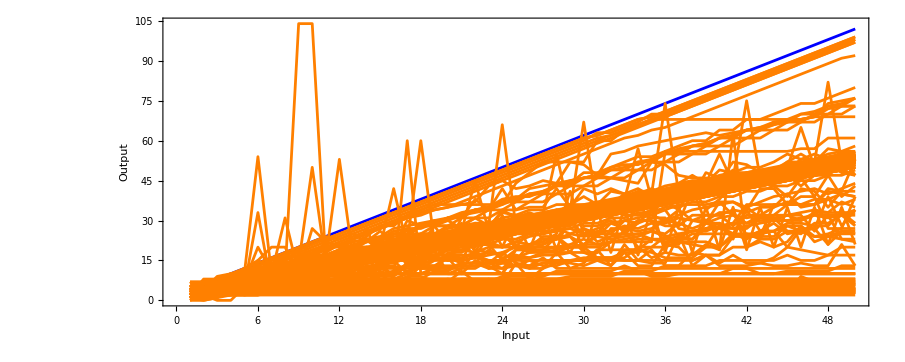

```mathematica
ListLinePlot[Join[{Table[ 2i+2, {i, 50}]}, Tooltip[Count[#, 1]&/@Table[CellularAutomaton[#Rule,{Append[Table[1, i], 2], 0},{{{100}}}], {i, 50}], ArrayPlot[CellularAutomaton[#Rule,{Append[Table[1, 15], 2], 0},60], ColorRules->colorrules]]&/@ ], PlotHighlighting->None, PlotStyle->Prepend[Table[Orange, 200], Blue], Frame->True, FrameLabel->{"Input", "Output"}, AspectRatio->.4]
```

#### Weird ff that worked

```mathematica
ParallelTable[SeedRandom[342550 + i];
AdaptiveCellularAutomaton[<|"Rule"->{0, 3, 1}, "Depth"->1000, 
"MutationFunction"->(RandomRuleMutation[#Rule, 1]&),
"FitnessFunction"-> (-Total[Abs[Table[CenterArray[#, Max[Length[#],2i]&[#]] - CenterArray[Table[1, 2i], Max[Length[#],2i]]&[CellularAutomaton[#1, {Append[Table[1, i], 2], 0}, {{{60}}}]] , {i, 5}]], 2]&)|>, "Final"], {i , 200}]
```

{<|Rule→{1694985738690,3,1},Fitness→-5|>,<|Rule→{3462488012790,3,1},Fitness→-11|>,<|Rule→{5716399877793,3,1},Fitness→-13|>,<|Rule→{7369160977971,3,1},Fitness→-4|>,<|Rule→{2250195838797,3,1},Fitness→-10|>,<|Rule→{7379855177778,3,1},Fitness→-5|>,<|Rule→{7354165831203,3,1},Fitness→-5|>,<|Rule→{3138600207504,3,1},Fitness→-5|>,<|Rule→{4742447275725,3,1},Fitness→-15|>,<|Rule→{1948487810385,3,1},Fitness→-5|>,<|Rule→{2013148699680,3,1},Fitness→-3|>,<|Rule→{2683224607779,3,1},Fitness→-9|>,<|Rule→{1754389857417,3,1},Fitness→-5|>,<|Rule→{3524425724490,3,1},Fitness→-3|>,<|Rule→{1341680911248,3,1},Fitness→-15|>,<|Rule→{4426257071310,3,1},Fitness→-4|>,<|Rule→{4091918405076,3,1},Fitness→-4|>,<|Rule→{6650883203508,3,1},Fitness→-4|>,<|Rule→{5215274523498,3,1},Fitness→-2|>,<|Rule→{2122829113194,3,1},Fitness→-11|>,<|Rule→{4011560853867,3,1},Fitness→-17|>,<|Rule→{827713133604,3,1},Fitness→-13|>,<|Rule→{5896661779575,3,1},Fitness→-4|>,<|Rule→{1940226214416,3,1},Fitness→-10|>,<|Rule→{2703498364101,3,1},Fitness→-2|>,<|Rule→{360429437925,3,1},Fitness→-12|>,<|Rule→{1936514623584,3,1},Fitness→-9|>,<|Rule→{4231348564149,3,1},Fitness→-10|>,<|Rule→{6748613802702,3,1},Fitness→-9|>,<|Rule→{4687556801415,3,1},Fitness→-3|>,<|Rule→{4181063119653,3,1},Fitness→-5|>,<|Rule→{7544566278549,3,1},Fitness→-7|>,<|Rule→{4153087315179,3,1},Fitness→-9|>,<|Rule→{2936007184005,3,1},Fitness→-11|>,<|Rule→{3902456953521,3,1},Fitness→-3|>,<|Rule→{2073666393708,3,1},Fitness→-11|>,<|Rule→{3747326450481,3,1},Fitness→-10|>,<|Rule→{705815778894,3,1},Fitness→-7|>,<|Rule→{3111378771834,3,1},Fitness→-24|>,<|Rule→{432755857422,3,1},Fitness→-9|>,<|Rule→{493437123468,3,1},Fitness→-4|>,<|Rule→{4380720136371,3,1},Fitness→-11|>,<|Rule→{599174365626,3,1},Fitness→-5|>,<|Rule→{859139633316,3,1},Fitness→-9|>,<|Rule→{3405023522268,3,1},Fitness→-7|>,<|Rule→{4486876897491,3,1},Fitness→-4|>,<|Rule→{3083945628954,3,1},Fitness→-5|>,<|Rule→{5224946178267,3,1},Fitness→-6|>,<|Rule→{5037378847842,3,1},Fitness→-11|>,<|Rule→{129476686047,3,1},Fitness→-4|>,<|Rule→{7539656125806,3,1},Fitness→-9|>,<|Rule→{7296115660947,3,1},Fitness→-4|>,<|Rule→{1160474652165,3,1},Fitness→-5|>,<|Rule→{2867957859663,3,1},Fitness→-6|>,<|Rule→{2798870116233,3,1},Fitness→-10|>,<|Rule→{1497200108127,3,1},Fitness→-5|>,<|Rule→{1462867967763,3,1},Fitness→-5|>,<|Rule→{1090595680803,3,1},Fitness→-9|>,<|Rule→{1871778502083,3,1},Fitness→-6|>,<|Rule→{4343409197514,3,1},Fitness→-4|>,<|Rule→{5366885134719,3,1},Fitness→-4|>,<|Rule→{3448776380154,3,1},Fitness→-13|>,<|Rule→{3153613331394,3,1},Fitness→-12|>,<|Rule→{6592937127615,3,1},Fitness→-7|>,<|Rule→{1818127933338,3,1},Fitness→-10|>,<|Rule→{2847037210938,3,1},Fitness→-7|>,<|Rule→{5467715581365,3,1},Fitness→-9|>,<|Rule→{2862097447707,3,1},Fitness→-5|>,<|Rule→{6578660316048,3,1},Fitness→-10|>,<|Rule→{4330962489411,3,1},Fitness→-10|>,<|Rule→{6256505401020,3,1},Fitness→-11|>,<|Rule→{2067254061102,3,1},Fitness→-6|>,<|Rule→{3217893206013,3,1},Fitness→-6|>,<|Rule→{3504626666409,3,1},Fitness→-5|>,<|Rule→{6633617248872,3,1},Fitness→-4|>,<|Rule→{6168807902799,3,1},Fitness→-6|>,<|Rule→{991761681657,3,1},Fitness→-7|>,<|Rule→{1585651727298,3,1},Fitness→-4|>,<|Rule→{1864676199600,3,1},Fitness→-6|>,<|Rule→{2543069725950,3,1},Fitness→-7|>,<|Rule→{2911736705982,3,1},Fitness→-6|>,<|Rule→{3081185782920,3,1},Fitness→-14|>,<|Rule→{5141134445769,3,1},Fitness→-6|>,<|Rule→{3922782556629,3,1},Fitness→-6|>,<|Rule→{1459870367688,3,1},Fitness→-14|>,<|Rule→{7057875961584,3,1},Fitness→-6|>,<|Rule→{4942578883680,3,1},Fitness→-3|>,<|Rule→{5151317443989,3,1},Fitness→-13|>,<|Rule→{3359451202077,3,1},Fitness→-6|>,<|Rule→{4556788904622,3,1},Fitness→-4|>,<|Rule→{3973362757137,3,1},Fitness→-6|>,<|Rule→{3431725431867,3,1},Fitness→-6|>,<|Rule→{2497037444991,3,1},Fitness→-4|>,<|Rule→{1153676959191,3,1},Fitness→-13|>,<|Rule→{2772761094432,3,1},Fitness→-6|>,<|Rule→{7072479119052,3,1},Fitness→-12|>,<|Rule→{1921841765889,3,1},Fitness→-4|>,<|Rule→{108484920522,3,1},Fitness→-9|>,<|Rule→{4091669865369,3,1},Fitness→-6|>,<|Rule→{4240051070178,3,1},Fitness→-2|>,<|Rule→{2986018985763,3,1},Fitness→-9|>,<|Rule→{1632917659086,3,1},Fitness→-15|>,<|Rule→{1431224727444,3,1},Fitness→-9|>,<|Rule→{5582879361336,3,1},Fitness→-5|>,<|Rule→{4664337915693,3,1},Fitness→-11|>,<|Rule→{5406172573107,3,1},Fitness→-5|>,<|Rule→{267987132531,3,1},Fitness→-10|>,<|Rule→{616279970304,3,1},Fitness→-8|>,<|Rule→{4003222605273,3,1},Fitness→-10|>,<|Rule→{4770186560925,3,1},Fitness→-12|>,<|Rule→{3717413683404,3,1},Fitness→-6|>,<|Rule→{2619899723844,3,1},Fitness→-9|>,<|Rule→{3497272340739,3,1},Fitness→-4|>,<|Rule→{1794940161690,3,1},Fitness→-5|>,<|Rule→{3074443539843,3,1},Fitness→-12|>,<|Rule→{6472905493644,3,1},Fitness→-10|>,<|Rule→{224333000265,3,1},Fitness→-15|>,<|Rule→{6377210051733,3,1},Fitness→-12|>,<|Rule→{3493910226591,3,1},Fitness→-10|>,<|Rule→{437462331777,3,1},Fitness→-6|>,<|Rule→{3437084204136,3,1},Fitness→-8|>,<|Rule→{7158668912829,3,1},Fitness→-10|>,<|Rule→{2319211204290,3,1},Fitness→-4|>,<|Rule→{7572445178475,3,1},Fitness→-12|>,<|Rule→{2778130706535,3,1},Fitness→-13|>,<|Rule→{6036119046333,3,1},Fitness→-6|>,<|Rule→{4490281709022,3,1},Fitness→-4|>,<|Rule→{1353642406794,3,1},Fitness→-10|>,<|Rule→{7369098913134,3,1},Fitness→-3|>,<|Rule→{1712017402788,3,1},Fitness→-9|>,<|Rule→{299368285353,3,1},Fitness→-6|>,<|Rule→{1972582800519,3,1},Fitness→-11|>,<|Rule→{5235306401034,3,1},Fitness→-5|>,<|Rule→{3961482034176,3,1},Fitness→-6|>,<|Rule→{5235079774881,3,1},Fitness→-12|>,<|Rule→{7119485031168,3,1},Fitness→-4|>,<|Rule→{1864336030875,3,1},Fitness→-8|>,<|Rule→{1301315754465,3,1},Fitness→-10|>,<|Rule→{4361471525460,3,1},Fitness→-5|>,<|Rule→{896856880752,3,1},Fitness→-6|>,<|Rule→{4812429025677,3,1},Fitness→-5|>,<|Rule→{3792500722716,3,1},Fitness→-10|>,<|Rule→{4442296657458,3,1},Fitness→-10|>,<|Rule→{3798551687454,3,1},Fitness→-8|>,<|Rule→{3718502421279,3,1},Fitness→0|>,<|Rule→{1074553216419,3,1},Fitness→-6|>,<|Rule→{35004140025,3,1},Fitness→-10|>,<|Rule→{6912708141537,3,1},Fitness→-5|>,<|Rule→{6845897847945,3,1},Fitness→-11|>,<|Rule→{5225075655669,3,1},Fitness→-6|>,<|Rule→{131417104296,3,1},Fitness→-6|>,<|Rule→{603966579864,3,1},Fitness→-5|>,<|Rule→{7296211563363,3,1},Fitness→-3|>,<|Rule→{4000995824283,3,1},Fitness→-8|>,<|Rule→{1963712322846,3,1},Fitness→-9|>,<|Rule→{3017932688364,3,1},Fitness→-6|>,<|Rule→{7102175657067,3,1},Fitness→-2|>,<|Rule→{6950013450804,3,1},Fitness→-16|>,<|Rule→{7051519866270,3,1},Fitness→-13|>,<|Rule→{3591759538041,3,1},Fitness→-4|>,<|Rule→{4687995362691,3,1},Fitness→-5|>,<|Rule→{2486669076717,3,1},Fitness→-10|>,<|Rule→{3941409773142,3,1},Fitness→-9|>,<|Rule→{3560639791770,3,1},Fitness→-11|>,<|Rule→{3833309744196,3,1},Fitness→-6|>,<|Rule→{1902006163827,3,1},Fitness→-11|>,<|Rule→{524665042236,3,1},Fitness→-5|>,<|Rule→{1066460259909,3,1},Fitness→-5|>,<|Rule→{6910254170982,3,1},Fitness→-4|>,<|Rule→{4457498951643,3,1},Fitness→-12|>,<|Rule→{1211435267337,3,1},Fitness→-13|>,<|Rule→{1138464029772,3,1},Fitness→-4|>,<|Rule→{5576156648190,3,1},Fitness→-13|>,<|Rule→{2744766182766,3,1},Fitness→-5|>,<|Rule→{5853859006086,3,1},Fitness→-6|>,<|Rule→{3623365450008,3,1},Fitness→-15|>,<|Rule→{4049431533684,3,1},Fitness→-4|>,<|Rule→{5348922746175,3,1},Fitness→-9|>,<|Rule→{3639588221952,3,1},Fitness→-4|>,<|Rule→{1644798520935,3,1},Fitness→-6|>,<|Rule→{1560235549626,3,1},Fitness→-6|>,<|Rule→{580377447675,3,1},Fitness→-6|>,<|Rule→{694536820374,3,1},Fitness→-5|>,<|Rule→{6386795996376,3,1},Fitness→-3|>,<|Rule→{6901876260261,3,1},Fitness→-9|>,<|Rule→{4632976984038,3,1},Fitness→-5|>,<|Rule→{1800382637679,3,1},Fitness→-12|>,<|Rule→{2128796879976,3,1},Fitness→-4|>,<|Rule→{3494086587411,3,1},Fitness→-4|>,<|Rule→{969863722005,3,1},Fitness→-5|>,<|Rule→{1258325125650,3,1},Fitness→-4|>,<|Rule→{4260811770135,3,1},Fitness→-15|>,<|Rule→{1351316533329,3,1},Fitness→-13|>,<|Rule→{536477237601,3,1},Fitness→-7|>,<|Rule→{2053854019161,3,1},Fitness→-15|>,<|Rule→{704472832302,3,1},Fitness→-8|>,<|Rule→{3895496163936,3,1},Fitness→-4|>,<|Rule→{5943338796591,3,1},Fitness→-9|>,<|Rule→{266224107861,3,1},Fitness→-13|>,<|Rule→{5549183705286,3,1},Fitness→-2|>}

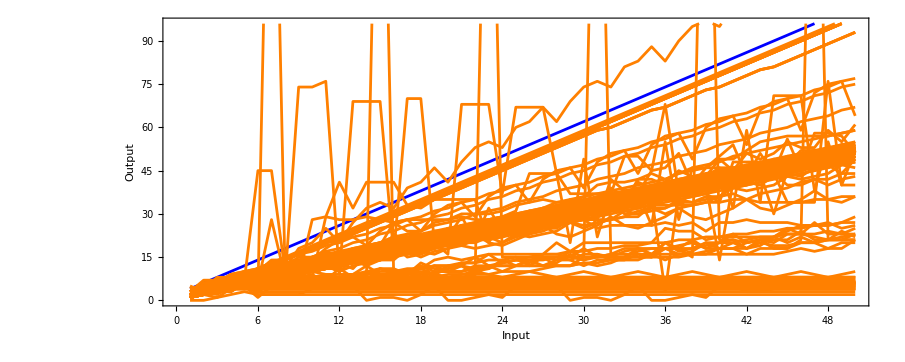

```mathematica
ListLinePlot[Join[{Table[ 2i+2, {i, 50}]}, Tooltip[Count[#, 1]&/@Table[CellularAutomaton[#Rule,{Append[Table[1, i], 2], 0},{{{300}}}], {i, 50}], ArrayPlot[CellularAutomaton[#Rule,{Append[Table[1, 15], 2], 0},60], ColorRules->colorrules]]&/@ ], PlotHighlighting->None, PlotStyle->Prepend[Table[Orange, 200], Blue], Frame->True, FrameLabel->{"Input", "Output"}, AspectRatio->.4]
```

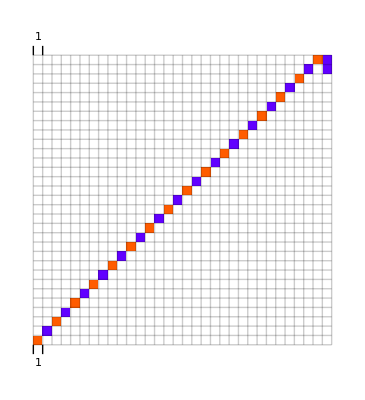
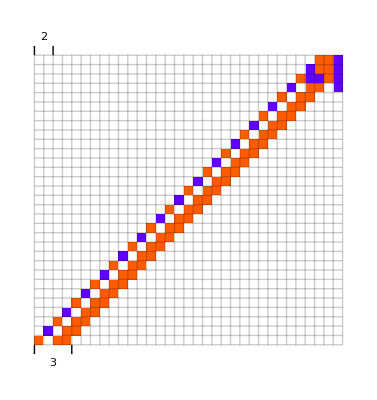
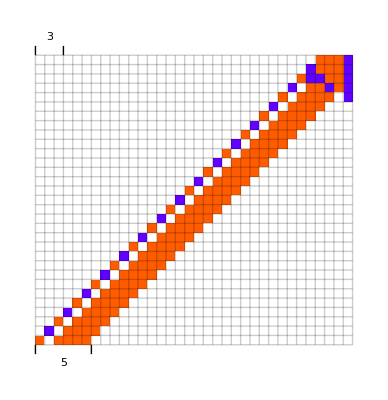
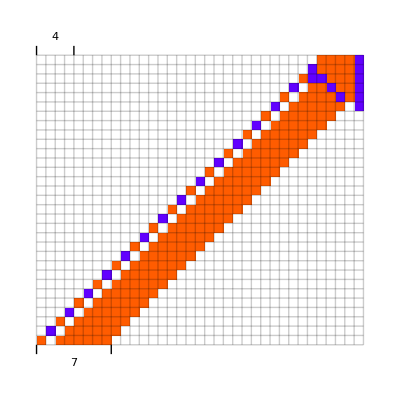
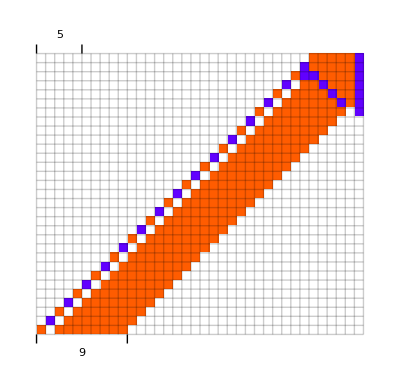
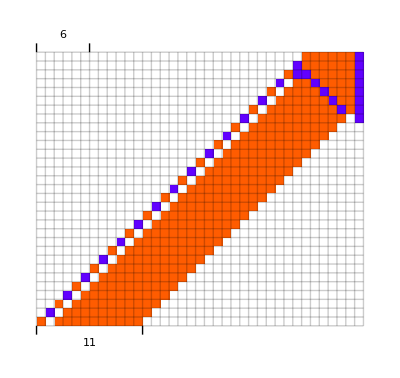
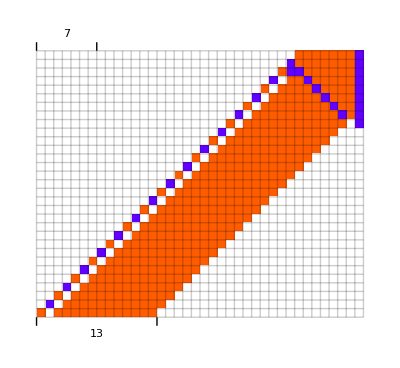
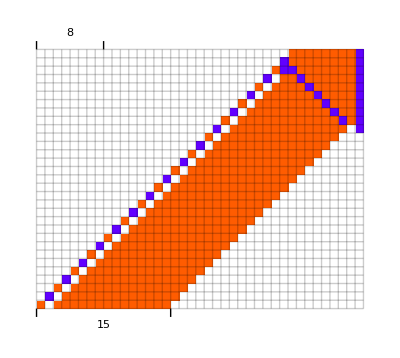

```mathematica
Row[Table[With[{ca = CellularAutomaton[#Rule,{Append[Table[1, i], 2], 0}, 30]},Show[ArrayPlot[ca, ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99],4->RGBColor[0, 0.56, 0],5->RGBColor[0, 0.56, 1]}, 
FrameTicksStyle->Directive[Thickness[.01], GrayLevel[.3]],Mesh->True, MeshStyle->Opacity[.2]],
Graphics[{Line[{{0, Length[ca]},{0, Length[ca] + 1}}],Line[{{0 + i, Length[ca]},{0 + i, Length[ca] + 1}}], Style[Text[ToString[i], {i /2, Length[ca] + 2}],10],
Sequence@@(Line[{{#, 0}, {#, -1}}]&/@MapAt[# -1&, nonzeroRange[Last[ca]], 1]),
Style[Text[ToString[Count[Last[ca], 1]], {Mean[MapAt[# -1&, nonzeroRange[Last[ca]], 1]], -2}],10]
}], PlotRange->All]], {i, 8}]&/@ [[Select[Differences[Count[#, 1]&/@Table[CellularAutomaton[#Rule,{Append[Table[1, i], 2], 0},{{{200}}}], {i, 50}]]&/@, AllTrue[#, # ==2&]&->"Index"]]]]
```